101

Analysis done!

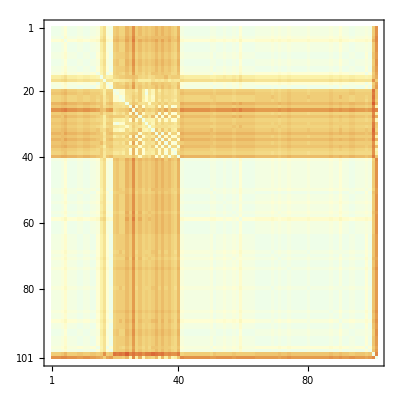

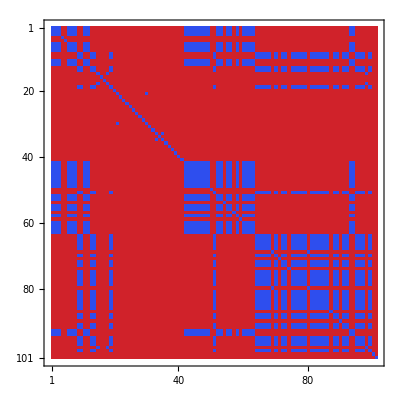

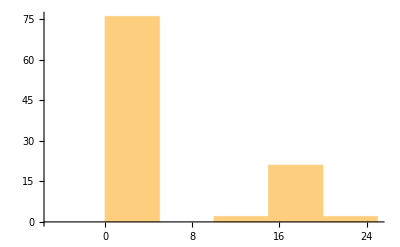

26

Clupea harengus NTD

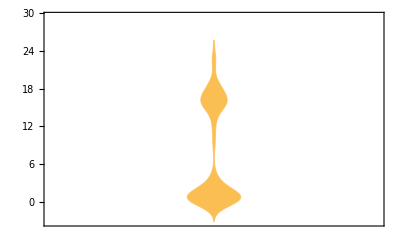

Average Edit Distance: 7.58259 +/- 7.81618

Median Edit Distance: 2. +/- 2.

NTD_DistributionGraph.pdf

```mathematica
(* Provide input file path *)

Datei="Unique species NTDs.fasta";

Sequenzen=Import[Datei,"Sequence"];
Header=Import[Datei,"Header"];
Length[Header]

Distances={};
Do[{a1=Sequenzen[[a]],
temp={};
Do[{b1=Sequenzen[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Sequenzen]}],
Distances=AppendTo[Distances,temp]
},{a,1,Length[Sequenzen]}]
Print[Style["Analysis done!",Bold,Blue]]


(* Plot the data *)

(* Matrix Plots *)
MatrixPlot[Distances,ColorFunction->"LightTemperatureMap"]
MatrixPlot[Distances,ColorFunction->"TemperatureMap",ColorFunctionScaling->False]

(* Identify most divergent species *)
Histogram[Distances[[1]]]
pos=Flatten[Position[Distances[[1]],Max[Distances[[1]]]]][[1]]
Header[[pos]]

(* Distribution graph *)
ExpGraphik=DistributionChart[{0,Flatten[Distances],0},
PlotRange->{{1,6},{Automatic,40}}]

UbDistances=Flatten[Distances];

Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[UbDistances]]," +/- ",
N[StandardDeviation[UbDistances]]]

Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[UbDistances]]," +/- ",
N[MedianDeviation[UbDistances]]]


SetDirectory[DirectoryName[Datei]];
Export["NTD_DistributionGraph.pdf",ExpGraphik]
```

Ailuropoda melanoleuca NTD | 1
Alligator sinensis NTD | 1
Amazona aestiva NTD | 1
Anas platyrhynchos NTD | 1
Apaloderma vittatum NTD | 1
Aptenodytes forsteri NTD | 1
Apteryx australis mantelli NTD | 1
Balaenoptera acutorostrata scammoni NTD | 1
Bos taurus NTD | 1
Callithrix jacchus NTD | 1
Calypte anna NTD | 1
Caprimulgus carolinensis NTD | 1
Cariama cristata NTD | 1
Cercocebus atys NTD | 1
Chaetura pelagica NTD | 1
Charadrius vociferus NTD | 1
Chlamydotis macqueenii NTD | 1
Chrysemys picta bellii NTD | 1
Chrysochloris asiatica NTD | 1
Colius striatus NTD | 1
Columba livia NTD | 1
Condylura cristata NTD | 1
Corvus cornix cornix NTD | 1
Cuculus canorus NTD | 1
Dasypus novemcinctus NTD | 1
Elephantulus edwardii NTD | 1
Equus caballus NTD | 1
Erinaceus europaeus NTD | 1
Eurypyga helias NTD | 1
Falco peregrinus NTD | 1
Felis catus NTD | 1
Ficedula albicollis NTD | 1
Gallus gallus NTD | 1
Heterocephalus glaber NTD | 1
Homo sapiens NTD | 1
Jaculus jaculus NTD | 1
Lepidothrix coronata NTD | 1
Loxodonta africana NTD | 1
Meleagris gallopavo NTD | 1
Melopsittacus undulatus NTD | 1
Microcebus murinus NTD | 1
Miniopterus natalensis NTD | 1
Mus musculus NTD | 1
Myotis lucifugus NTD | 1
Nestor notabilis NTD | 1
Nomascus leucogenys NTD | 1
Octodon degus NTD | 1
Ophiophagus hannah NTD | 1
Opisthocomus hoazin NTD | 1
Ornithorhynchus anatinus NTD | 1
Orycteropus afer afer NTD | 1
Ovis aries musimon NTD | 1
Ovis aries NTD | 1
Pantholops hodgsonii NTD | 1
Pelecanus crispus NTD | 1
Pelodiscus sinensis NTD | 1
Phaethon lepturus NTD | 1
Phoenicopterus ruber ruber NTD | 1
Picoides pubescens NTD | 1
Pongo abelii NTD | 1
Pseudopodoces humilis NTD | 1
Pterocles gutturalis NTD | 1
Pteropus alecto NTD | 1
Pygoscelis adeliae NTD | 1
Python bivittatus NTD | 1
Sarcophilus harrisii NTD | 1
Sorex araneus NTD | 1
Struthio camelus australis NTD | 1
Sturnus vulgaris NTD | 1
Sus scrofa NTD | 1
Taeniopygia guttata NTD | 1
Tauraco erythrolophus NTD | 1
Thamnophis sirtalis NTD | 1
Tinamus guttatus NTD | 1
Ursus maritimus NTD | 1
Zonotrichia albicollis NTD | 1
Astyanax mexicanus NTD | 2
Austrofundulus limnaeus NTD | 2
Callorhinchus milii NTD | 2
Clupea harengus NTD | 2
Cyprinodon variegatus NTD | 2
Esox lucius NTD | 2
Ictalurus punctatus NTD | 2
Kryptolebias marmoratus NTD | 2
Larimichthys crocea NTD | 2
Lepisosteus oculatus NTD | 2
Nothobranchius furzeri NTD | 2
Notothenia coriiceps NTD | 2
Oreochromis niloticus NTD | 2
Oryzias latipes NTD | 2
Poecilia formosa NTD | 2
Poecilia mexicana NTD | 2
Pundamilia nyererei NTD | 2
Pygocentrus nattereri NTD | 2
Salmo salar NTD | 2
Sinocyclocheilus anshuiensis NTD | 2
Sinocyclocheilus grahami NTD | 2
Sinocyclocheilus rhinocerous NTD | 2
Stegastes partitus NTD | 2
Xenopus laevis NTD | 2
Xiphophorus maculatus NTD | 2

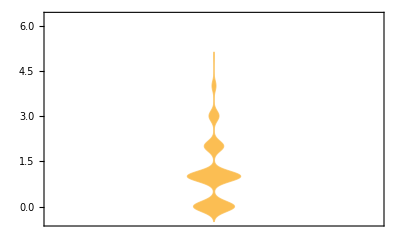

Average Edit Distance: 1.10769 +/- 1.07703

Median Edit Distance: 1. +/- 1.

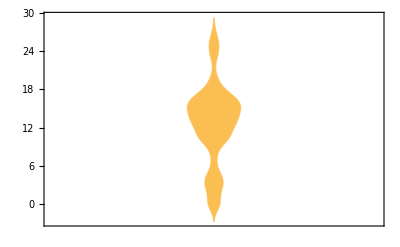

Average Edit Distance: 12.7232 +/- 6.14686

Median Edit Distance: 13. +/- 3.

```mathematica
(* Cluster analysis*)

TableForm[SortBy[Transpose[{Header,ClusteringComponents[Distances,2][[1]]}],Last]]
ClusterSeq=SortBy[Transpose[{Sequenzen,ClusteringComponents[Distances,2][[1]]}],Last];

(* Analyze sequences in cluster 1*)
TempCluster1=Select[ClusterSeq,#[[2]]==1&];
Cluster1=Transpose[TempCluster1][[1]];
Cl1dist={};
Do[{a1=Cluster1[[a]],
temp={};
Do[{b1=Cluster1[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Cluster1]}],
Cl1dist=AppendTo[Cl1dist,temp]
},{a,1,Length[Cluster1]}]
DistributionChart[{0,Flatten[Cl1dist],0},
PlotRange->{{1,6},{Automatic,40}}]
Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[Flatten[Cl1dist]]]," +/- ",
N[StandardDeviation[Flatten[Cl1dist]]]]
Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[Flatten[Cl1dist]]]," +/- ",
N[MedianDeviation[Flatten[Cl1dist]]]]

(* Analyze sequences in cluster 2*)
TempCluster2=Select[ClusterSeq,#[[2]]==2&];
Cluster2=Transpose[TempCluster2][[1]];
Cl2dist={};
Do[{a1=Cluster2[[a]],
temp={};
Do[{b1=Cluster2[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Cluster2]}],
Cl2dist=AppendTo[Cl2dist,temp]
},{a,1,Length[Cluster2]}]
DistributionChart[{0,Flatten[Cl2dist],0},
PlotRange->{{1,6},{Automatic,40}}]
Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[Flatten[Cl2dist]]]," +/- ",
N[StandardDeviation[Flatten[Cl2dist]]]]
Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[Flatten[Cl2dist]]]," +/- ",
N[MedianDeviation[Flatten[Cl2dist]]]]
```